```mathematica
parameters=<|"μrange"->{1/20,1/2},"δμ"->1/100,"nrange"->{0,4},"δn"->1,"mrange"->{1,4},"δm"->1,"EndingX"->8000,"StartingX"->1/10000,"precision"->26,"omegaRes"->500,"MaxInterationsMinimization"->1000,"RadialIntegratorMaxStep"->1000000,"RadialIntegratorPrecisionGoal"->8,"OptimizationPrecision"->30,"OptimizationAccuracy"->18,"StartingR"->1.4359898943540674,"EndingR"->8001+(√19)/10,"branch"->1,"KMax"->4,"ϵ"->1/10000,"μNv"->11/100,"m"->1,"η"->0,"n"->0,"l"->0,"s"->-1,"χ"->9/10,"M"->1|>;
parameters["EndingX"]=calcEndingX[parameters];

$FKKSRoot = NotebookDirectory[]<>"../";
$SolutionPath = $FKKSRoot<>"Solutions/";
PlotPath = $FKKSRoot<>"Plots/";
Import[FileNameJoin[{$FKKSRoot, "Packages", "HelperFunctions.wl"}]]
Import[FileNameJoin[{$FKKSRoot, "Packages", "KerrWithProca.wl"}]]
samp = getResults[$SolutionPath, {{"m",1},{"n",0}, {"μNv", "11_100"}, {"branch",1}}]//First;
ωval = samp["Solution", "ω"];
νval = samp["Solution", "ν"];
```

0.109335+1.21829×10^-7 ⅈ

Minimization Results: <|"ω" -> 0.1093138447908563 + 1.5767942870967203*^-7*I, "ν" -> -0.12174952167373404 - 7.734448971530573*^-8*I|>

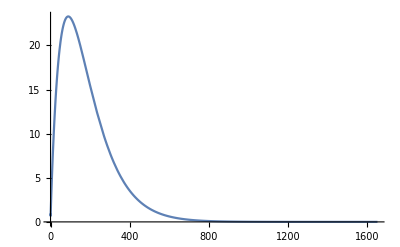

```mathematica
WatchEvaluation = True;
SaveToDisk = False;


printData=parameters[[{"ϵ", "μNv", "m", "η", "n", "l", "s", "χ"}]];

Messenger = "";
If[WatchEvaluation,Dynamic[Messenger]]
If[WatchEvaluation, Dynamic[RMMessenger]]

(*Minimization using Nelder Mead*)
Messenger=Style["Performing Minimization",Blue, Italic, 24];
minimizetimestart = AbsoluteTime[];
omegaGuess = N[omegaNRNonRel[parameters] + I*omegaNINonRel[parameters]]
nuGuess = getNuValue[omegaGuess, parameters,nuNNonRel[omegaGuess,parameters]]//N;
omegaBoundarySize = 1/2*(omegaNRNonRel[ReplacePart[parameters,"n"->parameters["n"]+1]] - omegaGuess//Re);
omegaBoundary = {omegaGuess - omegaBoundarySize, omegaGuess+omegaBoundarySize};
(*Perform minimization*)
MinimizationResults=RadialMinimize[omegaGuess,  nuGuess, omegaBoundary,  parameters, WatchEvaluation];
If[WatchEvaluation,Print["Minimization Results: "<>ToString[MinimizationResults//N, InputForm]]];

With[{radsol = getRadialSolution[MinimizationResults["ω"], MinimizationResults["ν"], parameters]},
Plot[radsol[r]//Re, {r,0.0001,parameters["EndingX"]}]
]
```

```mathematica
parameters=<|"μrange"->{1/20,1/2},"δμ"->1/100,"nrange"->{0,4},"δn"->1,"mrange"->{1,4},"δm"->1,"EndingX"->8000,"StartingX"->1/10000,"precision"->26,"omegaRes"->500,"MaxInterationsMinimization"->1000,"RadialIntegratorMaxStep"->1000000,"RadialIntegratorPrecisionGoal"->8,"OptimizationPrecision"->10,"OptimizationAccuracy"->18,"StartingR"->1.4359898943540674,"EndingR"->8001+(√19)/10,"branch"->1,"KMax"->4,"ϵ"->1/10000,"μNv"->11/100,"m"->1,"η"->0,"n"->0,"l"->0,"s"->-1,"χ"->9/10,"M"->1|>;
```

```mathematica
If[WatchEvaluation, Dynamic[RMMessenger]]

(*Minimization using Nelder Mead*)
omegaGuess = N[omegaNRNonRel[parameters] + I*omegaNINonRel[parameters]];
nuGuess = getNuValue[omegaGuess, parameters,nuNNonRel[omegaGuess,parameters]]//N;
omegaBoundarySize = 1/2*(omegaNRNonRel[ReplacePart[parameters,"n"->parameters["n"]+1]] - omegaGuess//Re);
omegaBoundary = {omegaGuess - omegaBoundarySize, omegaGuess+omegaBoundarySize};

ωGuess = omegaGuess;
SimplexBase = {ωGuess // Re, ωGuess // Im} // ToPrecision[parameters];
SimplexNodeOne = SimplexBase - {(omegaBoundary[[2]] - ωGuess)/parameters["omegaRes"], 0} // Re// ToPrecision[parameters];
SimplexNodeTwo = SimplexBase - {0, 10 ^ (Log10[Abs @ Im[ωGuess ]] - 1)}// ToPrecision[parameters];
InitialSimplex = {SimplexBase, SimplexNodeOne, SimplexNodeTwo
            };
MinimizationConstraints = ToPrecision[parameters][{10*Im[ωGuess]> ψ >Im[ωGuess]/10&&parameters["μNv"]^2>ξ^2+ψ^2&&Re[omegaBoundary[[2]]]>ξ>Re[omegaBoundary[[1]]]}];
Dynamic[CurrentIteration]
CurrentIteration=1;
$KWPMinimizationMethod={"NelderMead", 
                              "PostProcess" -> False, 
                              "InitialPoints" -> InitialSimplex,
		    "Tolerance"->0
                              };

method1 = {"NelderMead",  "PostProcess" -> False, "InitialPoints" -> InitialSimplex,"Tolerance"->0};
With[{constraints = ToPrecision[parameters][{100*Im[ωGuess]> ψ >10^-12&&parameters["μNv"]^2>ξ^2+ψ^2&&Re[omegaBoundary[[2]]]>ξ>Re[omegaBoundary[[1]]]}],
method = method1
},

res = NMinimize[
                    {Hold @ functomin[parameters][{ξ, ψ}], 
                    Sequence@@constraints
                    },
                    {ξ, ψ},
                    Method -> method,
                    WorkingPrecision -> 36,
                    EvaluationMonitor :>(RMMessenger = ToPrecision[parameters][ξ + I * ψ];CurrentIteration++;),
                    MaxIterations -> parameters["MaxInterationsMinimization"]
                ]//Last
]
ωval = (ξ+I*ψ)/.res;
νval = getNuValue[ωval, parameters, nuNNonRel[ωval, parameters]];
rad = getRadialSolution[ωval, νval, parameters];

Plot[rad[r]//Re, {r,0.0001, rad["Domain"]//First//Last}, PlotRange->All]
```

```mathematica
ωval
ωGuess
11/100//N
```

```mathematica
res//First//Last;
ωval = %[[1]]+I*%[[2]]
νval = getNuValue[ωval, parameters, nuNNonRel[ωval, parameters]]
rad = getRadialSolution[ωval, νval, parameters];
Plot[rad[r]//Re, {r,0.0001, 8000}]
```

```mathematica
dom = res//First;
ran = functomin[parameters]/@dom;
points = Thread[{dom,ran}];
```

```mathematica
Flatten[#,1]&/@points//Last
```

```mathematica
ParallelEvaluate[Off[ClebschGordan::phy];Off[ClebschGordan::tri]];
tab = Parallelize@Table[{i,functomin[parameters][{ωval//Re,i}]}, {i,10^-12,10^-9,10^-11}];
```

```mathematica
ListPlot[tab]
res//First//Last;
Print["ωval1"];

res//First//Last
ωval1 = %[[1]]+I*10^-9
νval = getNuValue[ωval1, parameters, nuNNonRel[ωval1, parameters]]
rad = getRadialSolution[ωval1, νval, parameters];
Print["At endingX"]
rad[parameters["EndingX"]]//Abs//Log10
functomin[parameters][{Re[ωval1], Im[ωval1]}]
Plot[rad[r]//Abs, {r,0.0001,8000}, PlotLabel->"Outside functomin"]
```

```mathematica
Manipulate[
Block[{ωvalt,νvalt},
ωvalt = ωval+ωrx+I*ωix;
νvalt = getNuValue[ωvalt,parameters,nuNNonRel[ωvalt,parameters]];
radsol = getRadialSolution[ωvalt, νvalt, parameters];
Row[{Plot[radsol[r]//Re, {r,0.0001,parameters["EndingX"]}, ImageSize->Medium, PlotRange->{0,20}], Spacer[20], ToString[ωvalt, InputForm]}]
],
{{ωrx,0},-0.001,0.001},
{{ωix,0},-10^-8,10^-8,10^-14}
]
```

```mathematica
parameters =<|"μrange"->{1/20,1/2},"δμ"->1/100,"nrange"->{0,4},"δn"->1,"mrange"->{1,4},"δm"->1,"EndingX"->8000,"StartingX"->1/10000,"precision"->26,"omegaRes"->1000,"MaxInterationsMinimization"->1000,"RadialIntegratorMaxStep"->1000000,"RadialIntegratorPrecisionGoal"->8,"OptimizationPrecision"->10,"OptimizationAccuracy"->18,"StartingR"->1.4359898943540674,"EndingR"->8001+(√19)/10,"branch"->1,"KMax"->4,"ϵ"->1/10000,"μNv"->1/20,"m"->1,"η"->0,"n"->0,"l"->0,"s"->-1,"χ"->9/10,"M"->1|>;
```

```mathematica
ωval
omegaBoundary
```

```mathematica
omegaGuess = (ξ+I*ψ)/.res;
omegaBoundary = {Re[ωval]-10^-4+I*10^-12, Re[ωval]+10^-4+I*10^-9}
funcwrapper[ω_?NumericQ]:=functomin[parameters][{Re[ω],Im[ω]}]
rootsol = FindRoot[
funcwrapper[ξ], 
{ξ,omegaGuess, Sequence@@omegaBoundary},
 WorkingPrecision->30, 
PrecisionGoal->10, 
AccuracyGoal->18,
MaxIterations->300]
```

```mathematica
ωval = ξ/.rootsol
νval = getNuValue[ωval, parameters, nuNNonRel[ωval, parameters]];
radsol = getRadialSolution[ωval, νval, parameters]
Plot[radsol[r]//Re, {r,0.0001,8000}]
```

```mathematica
ωval
```

```mathematica
ωval//Norm
Norm[1+I*2]
```